| Estimate | Standard Error | t-Statistic | P-Value
1 | 135.463 | 6.61659 | 20.4733 | 0.0000336144
x | -57.8794 | 2.82416 | -20.4944 | 0.0000334771

{q→135.463,Δq→6.61659}

{dc→{3.54976,-69.9944},Δdc→0.0561495}

{dac→{9.62545,18.1889},Δdac→0.481273}

{Φ→0.1076,ΔΦ→0.0060224}

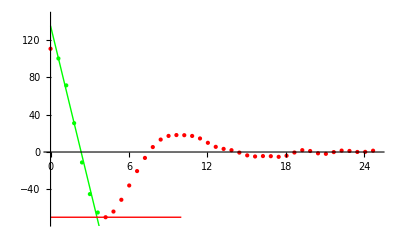

{q→151.827,Δq→4.16198}

{dc→{3.95112,-94.0629},Δdc→0.0446341}

{dac→{10.8286,24.2523},Δdac→0.54143}

{Φ→0.122669,ΔΦ→0.00392974}

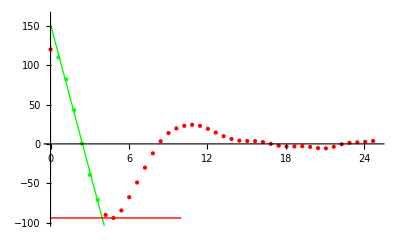

```mathematica
(*Import Data from files*)
Clear[lFit, Q, Φ, ρ];
prefix = "PET-";
sample = "140";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".cor","Table"];


(*Split Data into parts for linear fit and for the rest*)
sampleSize = 6;
linearData =  Take[rawData, {2,sampleSize}];
afterLinearData =  Take[rawData, -(Length[rawData ] - sampleSize)];
nonLinearData = Join[Take[rawData, 1], afterLinearData];

(*Find Min and Max of data, also find 2nd local max*)
minMax = {First@SortBy[rawData,Last], Last@SortBy[rawData,Last]};
localMax = Last@SortBy[afterLinearData,Last];

(*Linear fit*)
lFit = LinearModelFit[linearData,x,x];
lFit["ParameterTable"]


(*Relevant points*)


Δq = lFit["ParameterTable"][[1]][[1]][[2]][[3]];
q = {"q"-> lFit["Function"][0], "Δq"->Δq}
Δm = lFit["ParameterTable"][[1]][[1]][[3]][[3]];
dcP = Solve[lFit["BestFit"]+Δq-Δm*x== minMax[[1]][[2]], x][[All, 1, 2]][[1]];
dcT = {Solve[lFit["BestFit"] == minMax[[1]][[2]], x][[All, 1, 2]][[1]], minMax[[1]][[2]]};
Δdc = dcT[[1]] - dcP;
dc = {"dc"->dcT, "Δdc"->Δdc}
dac = {"dac"->localMax, "Δdac"-> localMax[[1]]*0.05}

ρ= 37.56;
Phi = Solve[lFit["Function"][0]== Φ(1-Φ)*ρ^2,Φ][[All, 1, 2]][[1]];
ΔPhi = Solve[lFit["Function"][0] + Δq== Φ(1-Φ)*ρ^2,Φ][[All, 1, 2]][[1]] - Phi;
{"Φ"->Phi,"ΔΦ"->ΔPhi}


Export[path<>"-Q-Dc-Dac-Dacy.txt", {q, dc, dac, dacy}, "Table"];
Export[path <> ".cor.txt", lFit["BestFit"], "String"];

(*Plot functions and data*)
Show[ListPlot[nonLinearData,PlotStyle->Red], ListPlot[linearData,PlotStyle->Green], Plot[{lFit["BestFit"]},{x,0,8}, PlotStyle-> Green], Plot[{minMax[[1]][[2]]},{x,0,10}, PlotStyle-> Red], PlotRange-> {{0,25},{minMax[[1]][[2]] - 5,lFit["Function"][0]+ 10}}]
```